```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;

datrotuwsoca=Flatten[Import["trot_0.4_nutcalca.dat"]];
datrotdwsoca=Flatten[Import["trot_0.4_ndtcalca.dat"]];
datrotuwsocb=Flatten[Import["trot_0.4_nutcalcb.dat"]];
datrotdwsocb=Flatten[Import["trot_0.4_ndtcalcb.dat"]];
```

```mathematica
impdiffdata=Table[Partition[(datrotuwsoca+datrotdwsoca),3][[i,1]] + Partition[(datrotuwsoca+datrotdwsoca),3][[i,2]]+ Partition[(datrotuwsoca+datrotdwsoca),3][[i,3]],{i,1,Nx*Ny}];

diffdata=impdiffdata;
```

```mathematica
impdiffdatb=Table[Partition[(datrotuwsocb+datrotdwsocb),3][[i,1]] + Partition[(datrotuwsocb+datrotdwsocb),3][[i,2]]+ Partition[(datrotuwsocb+datrotdwsocb),3][[i,3]],{i,1,Nx*Ny}];

diffdatb=impdiffdatb;
```

```mathematica
plotdiffdata=Partition[Riffle[diffdata,Table[0,{i,Length[diffdata]}]],2*Sqrt[Length[diffdata]]];
plotdiffdatb=Partition[Riffle[Table[0,{i,Length[diffdatb]}],diffdatb],2*Sqrt[Length[diffdatb]]];
plotdiffdatab=Riffle[plotdiffdata,plotdiffdatb];
```

```mathematica
length=Sqrt[Length[diffdata]];
hlength=IntegerPart[length/2];
```

```mathematica
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1);
l = l+1;
coorda[l] = {xpos,ypos};
];];
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1)+1;
l = l+1;
coordb[l] = {xpos,ypos};
];];
rownumber=7;
countatom=7;

midatom=(nx*rownumber + countatom)+1;
midcoord=coorda[midatom];
```

```mathematica
For[l=1,l<=nx*ny,l++,
newcoorda[l] = coorda[l] - midcoord];
For[l=1,l<=nx*ny,l++,
newcoordb[l] = coordb[l] - midcoord];

ndiffdata = Table[Flatten[{newcoorda[l] ,diffdata[[l]],l}],{l,1,nx*ny}];
ndiffdatb = Table[Flatten[{newcoordb[l] ,diffdatb[[l]],nx*ny+l}],{l,1,nx*ny}];
```

```mathematica
alldiffdata= Join[ndiffdata ,ndiffdatb ];
limval = alldiffdata[[All,3]];
minval=3.96;
maxval=3.97;
```

```mathematica
squarelength=3;
xmax=squarelength;
xmin=-squarelength;
ymax=squarelength;
ymin=-squarelength;

posmidcoord = {0,0};
coordx1 = xmin;
coordy1 = ymin;
coordx2 = xmax;
coordy2 = ymin;
coordx3 = xmax;
coordy3 = ymax;
coordx4 = xmin;
coordy4 = ymax;

squareline=
{Blue,Thickness[0.01],Line[{{{coordx1,coordy1},{coordx2,coordy2}},{{coordx2,coordy2},{coordx3,coordy3}},{{coordx3,coordy3},{coordx4,coordy4}},{{coordx4,coordy4},{coordx1,coordy1}}}]};
```

```mathematica
rmvpoints1=DeleteCases[Table[If[alldiffdata[[i,1]]>coordx3,pt=Null,If[alldiffdata[[i,2]]>coordy3,pt=Null,pt={alldiffdata[[i,1]],alldiffdata[[i,2]],alldiffdata[[i,3]],alldiffdata[[i,4]]}]];pt,{i,1,Length[alldiffdata]}],Null];

rmvpoints2=DeleteCases[Table[If[rmvpoints1[[i,1]]<coordx1,pt=Null,If[rmvpoints1[[i,2]]<coordy1,pt=Null,pt={rmvpoints1[[i,1]],rmvpoints1[[i,2]],rmvpoints1[[i,3]],rmvpoints1[[i,4]]}]];pt,{i,1,Length[rmvpoints1]}],Null];
```

```mathematica
slimval=rmvpoints2[[All,3]];
sminval=Min[slimval];
smaxval=Max[slimval];
spointlegend=BarLegend[{"Rainbow",{sminval,smaxval}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]}];
```

```mathematica
crldosa=DeleteCases[Table[If[rmvpoints2[[l,4]]<=nx*ny,pt={rmvpoints2[[l,1]],rmvpoints2[[l,2]],rmvpoints2[[l,4]]},pt=Null];pt,{l,1,Length[rmvpoints2]}],Null];
ldosa=crldosa[[All,3]];

crldosb=DeleteCases[Table[If[rmvpoints2[[l,4]]>nx*ny,pt={rmvpoints2[[l,1]],rmvpoints2[[l,2]],rmvpoints2[[l,4]]},pt=Null];pt,{l,1,Length[rmvpoints2]}],Null];
ldosb=crldosb[[All,3]];
ivalldos=Join[Flatten[Table[(ldosa[[l]]-1)*3+n+nx*ny*3*2*s,{l,1,Length[ldosa]},{s,0,1},{n,1,3}]],
Flatten[Table[(ldosb[[l]]-1)*3+n+nx*ny*3*2*s,{l,1,Length[ldosb]},{s,0,1},{n,1,3}]]];
Export["ivalldos.dat",ivalldos];
ldosdat=Import["wmax3.5_Ny15_Nx15_eta0.12_Ns40_ldostotal.dat"];
plldosdat=Partition[ldosdat[[All,2]],6];
fnplldosdat=Table[Total[plldosdat[[i]]],{i,1,Length[plldosdat]}];
```

```mathematica
ldoscoorda = crldosa[[All,{1,2}]];
ldoscoordb = crldosb[[All,{1,2}]];
fnldoscoordwor=Join[ldoscoorda,ldoscoordb];
fnldoscoord=fnldoscoordwor;
```

```mathematica
ldosminval=1.6;
ldosmaxval=1.75;
spointlodslegend=BarLegend[{"Rainbow",{ldosminval,ldosmaxval}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]}];
```

```mathematica
avldos=(ldosminval+ldosmaxval)/2;
k1max=100;
k2max=100;
For[k1=-k1max/2,k1≤k1max/2,k1++,
For[k2=-k2max/2,k2≤k2max/2,k2++,
kx=2Pi*k1/(k1max);
ky=2Pi*k2/(k2max);
mdiffdat=0;
For[i=1,i≤Length[fnldoscoord],i++,
mdiffdat=mdiffdat+(fnplldosdat[[i]]-avldos)*(Exp[I*(kx*fnldoscoord[[i,1]]+ky*fnldoscoord[[i,2]])])];
mdiff[k1,k2]=mdiffdat;]]
```

```mathematica
ftmin=Min[Table[Abs[mdiff[k1,k2]],{k2,-k2max/2,k2max/2},{k1,-k1max/2,k1max/2}]];
ftmax=Max[Table[Abs[mdiff[k1,k2]],{k2,-k2max/2,k2max/2},{k1,-k1max/2,k1max/2}]];
```

```mathematica
Clear[b,x]
nonorthleg=BarLegend["SunsetColors",LabelStyle->{Black,24}];
```

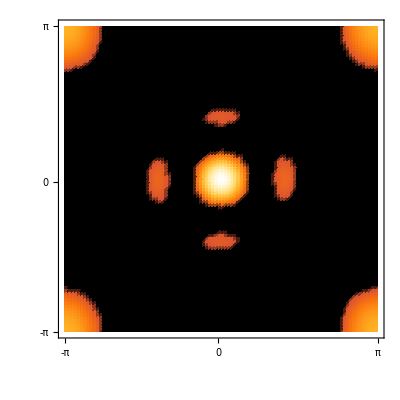

```mathematica
b1=ListDensityPlot[SetAccuracy[(1.3)Table[If[Abs[mdiff[k1,k2]]<=ftmin,ftmin,If[Abs[mdiff[k1,k2]]>=ftmax,ftmax,Abs[mdiff[k1,k2]]]],{k2,-k2max/2,k2max/2},{k1,-k1max/2,k1max/2}],0],PlotRange->All,
LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]},
PlotRangeClipping -> False,
FrameTicks->{{{{1,"-π"},{k1max/2,"0"},{k1max+1,"π"}},{{1,Null},{k1max/2,Null},{k1max+1,Null}}},{{{1,"-π"},{k2max/2,"0"},{k2max+1,"π"}},{{1,Null},{k2max/2,Null},{k2max+1,Null}}}},
FrameTicksStyle->Directive[FontFamily->"TimesNewRoman",Black,25],
Epilog -> {Rotate[Text[Style[Subscript[K,y],25],{-12,50.7}],Pi/2],Text[Style[Subscript[K,x],25],{50, -15}]},ImagePadding->{{49,15},{65,17}},
ColorFunction->"SunsetColors",ImageSize->400] 
Export["ldos_charge_ordering_momentum_space.png",b1];
Export["nonorthleg.png",nonorthleg];
```